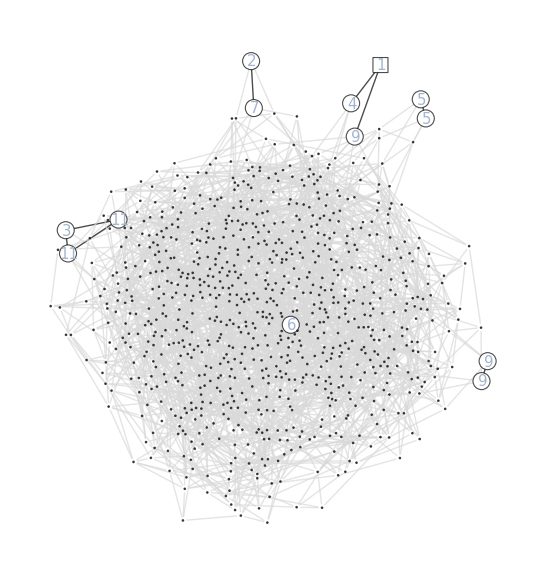

```mathematica
M=12;
minnorms=Import[NotebookDirectory[] <> "SupsingMinnorms.txt", "Table"];
edges=Import[NotebookDirectory[] <> "SupsingEdges.txt", "Table"];

(*Get rid of loops and multiple edges. The result will not be an accurate isogeny graph but will be easier to read*)
prunedEdges={};
For[i=1,i≤Length[edges],i++,
If[edges⟦i⟧⟦1⟧>edges⟦i⟧⟦2⟧&&Not[MemberQ[prunedEdges,edges⟦i⟧⟦1⟧<->edges⟦i⟧⟦2⟧]],AppendTo[prunedEdges,edges⟦i⟧⟦1⟧<->edges⟦i⟧⟦2⟧]]];

(*Uncomment the section below to apply a random permutation to the vertices; this allows Mathematica to try out different layouts for the graph*)
(*perm=RandomPermutation[Length[minnorms]];
minnorms=Permute[minnorms,perm];
prunedEdges=PermutationReplace[prunedEdges,perm];*)

(* "highlight" = M-small vertices, "dimmer" = remaining vertices *)
highlight=Select[Table[i,{i,1,Length[minnorms]}],minnorms⟦#⟧⟦1⟧≤M&];
dimmer=Select[Table[i,{i,1,Length[minnorms]}],minnorms⟦#⟧⟦1⟧>M&];

(*Generate the graph*)
Graph[prunedEdges,
(*Highlight edges between two M-small vertices*)
EdgeStyle->Table[prunedEdges⟦i⟧->If[MemberQ[highlight,prunedEdges⟦i⟧⟦1⟧]&&MemberQ[highlight,prunedEdges⟦i⟧⟦2⟧],Black,LightGray],{i,1,Length[prunedEdges]}],

(*Size and color of vertex based on whether it is M-small or not*)
VertexSize->Table[i->If[MemberQ[highlight,i],5.5,0.5],{i,1,Length[minnorms]}],
VertexStyle->Table[i->If[MemberQ[highlight,i],White,Gray],{i,1,Length[minnorms]}],

(*Label the M-small vertices*)
VertexLabelStyle->Table[highlight⟦i⟧->Directive[15, FontFamily->"CMU Serif"],{i,1,Length[highlight]}],
VertexLabels->Table[highlight⟦i⟧->Placed[minnorms⟦highlight⟦i⟧⟧⟦1⟧,{.55,.45}],{i,1,Length[highlight]}],

(*Make the vertex a square if it has an M-small automorphism*)
VertexShapeFunction->Table[i->If[minnorms⟦i⟧⟦1⟧==1,"Square",Automatic],{i,1,Length[minnorms]}]
]
```